## Special Functions and Orthogonal Polynomials

Student IDs = { #_1,#_2 } | Total Mark = mark | Marker =

## Syntax Reminders

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

For numerical expressions:  exact input ⟹ exact output,  approx input ⟹ approx output

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

### Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively one can use a Palette such as the Basic Math Assistant.

### Replacement Rules

Solutions to equations are returned as a list of lists of replacement rules:

```mathematica
sol=Solve[{a x^2+b y==0,c x+d y==0},{x,y}]
```

{{y→0,x→0},{y→-(b c^2)/(a d^2),x→(b c)/(a d)}}

To use the solutions, the ReplaceAll (/.) command is used. Here we substitute both solutions into both equations:

```mathematica
{a x^2+b y==0,c x+d y==0}/.sol
```

(True | True
True | True)

Substitute the second (or Last) solution into the variable x:

```mathematica
x/.sol⟦2⟧
```

(b c)/(a d)

Remove this definition:

```mathematica
Remove[sol]
```

### Protected Symbols

Certain symbols, such as D (which denotes the partial derivative) are protected:

```mathematica
D=2
```

Set::wrsym: Symbol D is Protected.

2

If one uses lower-case letters this problem is avoided.

An alternative is to use, say, script letters, available in the SpecialCharacters palette:

```mathematica
𝒟=2
```

2

Note that most special characters have Esc aliases (or keyboard shortcuts):  eg  𝒟 ← EscscDEsc,  while  𝔻 ← EscdsDEsc  etc…

### Basic List Operations

One can extract parts of an expression expr using Part or using the shorthand form expr[[n]] or expr⟦n⟧, with ⟦ ← Esc[[Esc :

```mathematica
{x,y,z}⟦2⟧
```

2

One can extract multiple entries using a list of indices:

```mathematica
{x,y,z}⟦{2,3,2,1}⟧
```

{y,z,y,x}

A matrix is a list of lists (rows).

Here is the first row of the matrix (a | b
c | d)={{a,b},{c,d}} :

```mathematica
({{a, b}, {c, d}})⟦1⟧
```

{a,b}

Here is the (2,1) element:

```mathematica
({{a, b}, {c, d}})⟦2,1⟧
```

Swap the first and second rows:

```mathematica
({{a, b}, {c, d}})⟦{2,1}⟧
```

The easiest way of swapping columns is to take the Transpose of the matrix first.

### Generating Matrices

One can construct matrices in a variety of ways. For now, we will do it either:

by hand, typing in a list of lists;

using the Basic Math Assistant palette;

using Insert ▸ Table/Matrix ▸ New…  ;

or using the Table command.

Construct a 2×3 matrix as a list of lists:

```mathematica
{{a,b,c},{d,e,f}}
```

(a | b | c
d | e | f)

Use Table to construct a general 4×6 matrix:

```mathematica
Table[Subscript[a, i,j],{i,4},{j,6}]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5) | a_(1,6)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5) | a_(2,6)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5) | a_(3,6)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5) | a_(4,6))

If you are not using TraditionalForm for output, you can use MatrixForm to display matrices:

```mathematica
MatrixForm@%
```

### Defining Functions

Define the function, f(x)=x^2+1:

```mathematica
f[x_]:=x^2+1
```

Note that the symbol f went from blue = undefined to black = defined.

Here is f(2):

```mathematica
f[2]
```

5

Here is f({x,y}):

```mathematica
f[{x,y}]
```

{x^2+1,y^2+1}

To see what definitions are associated with a symbol, use ?

```mathematica
?f
```

Global`f

f[x_]:=x^2+1

Clear this definition:

```mathematica
Clear[f]
```

The symbol f has now returned to being blue:

```mathematica
?f
```

Global`f

### Defining Vector Functions

Define g(x,y)=(x y,x^2-y^2), a vector function (or map) g:ℝ^2→ℝ^2:

```mathematica
g[{x_,y_}]:={x y,x^2-y^2}
```

Compute g(a,b):

```mathematica
g[{a,b}]
```

{a b,a^2-b^2}

Note that g takes a vector and returns a vector. This is useful when composing such functions.

Compute g∘g(x,y):

```mathematica
g@g[{x,y}]//Simplify
```

{x y (x^2-y^2),-x^4+3 x^2 y^2-y^4}

Remove this definition:

```mathematica
Clear[g]
```

## Special Functions

The zeroth-order Bessel function J_0(z) can be expressed as an infinite sum (its Maclaurin series),

J_0(x)==∑_(k=0)^∞ 1/(k!)^2(-x^2/4)^k

Zeros of J_0(z)

Verify that the sum gives J_0(x). [1 Mark]

Plot J_0(x) over -15≤x≤15. What is the symmetry of this function? What is the approximate spacing of the roots of J_0(x)? [2 Marks]

Use these observations with FindRoot to find accurate numerical values of the first 50 positive roots of J_0(x). Compare your values to the built-in function BesselJZero. [2 Marks]

Solution

Verify that the sum gives J_0(x):

```mathematica
Subscript[J, 0](x)==∑_(k=0)^∞ ((-x^2/4)^k)/(k!)^2
```

True

Plot J_0(x) over -15≤x≤15.

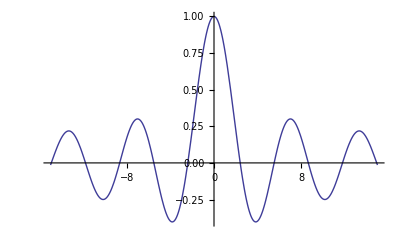

```mathematica
Plot[Subscript[J, 0](x),{x,-15,15}]
```

J_0(x) is even. The separation of the zeros is slightly larger than 3, approximately π.

Use FindRoot with initial guess spaced by π to obtain accurate numerical values of the first 50 positive roots of J_0(x):

```mathematica
𝒿=x/.FindRoot[Subscript[J, 0](x),{x,π Range[50]},WorkingPrecision->20]
```

{2.4048255576957727686,5.5200781102863106486,8.653727912911012217,11.791534439014281614,14.930917708487785948,18.071063967910922543,21.211636629879258959,24.352471530749302737,27.493479132040254796,30.634606468431975118,33.775820213573568684,36.91709835366404398,40.058425764628239295,43.199791713176730358,46.341188371661814019,49.482609897397817174,52.624051841114996029,55.765510755019979312,58.906983926080942133,62.048469190227169883,65.189964800206860441,68.331469329856798271,71.472981603593732825,74.614500643701837884,77.756025630388055038,80.897555871137627864,84.039090776938190158,87.180629843641153651,90.322172637210480056,93.463718781944774171,96.605267950996268778,99.74681985868059647,102.8883742541947946,106.02993091645161551,109.17148964980538355,112.31305028049490963,115.45461265366693963,118.59617663087253172,121.73774208795096297,124.87930891323294605,128.02087700600832408,131.16244627521391461,134.3040166383054661,137.44558802028427779,140.58716035285429655,143.72873357368973253,146.87030762579664959,150.01188245695475749,153.15345801922789249,156.29503426853352382}

Compare these values to the built-in function BesselJZero (note that you can use Range):

```mathematica
N[BesselJZero[0,Range[50]],20]
```

{2.4048255576957727686,5.5200781102863106496,8.653727912911012217,11.791534439014281614,14.930917708487785948,18.071063967910922543,21.211636629879258959,24.352471530749302737,27.493479132040254796,30.634606468431975118,33.775820213573568684,36.91709835366404398,40.058425764628239295,43.199791713176730358,46.341188371661814019,49.482609897397817174,52.624051841114996029,55.765510755019979312,58.906983926080942133,62.048469190227169883,65.189964800206860441,68.331469329856798271,71.472981603593732825,74.614500643701837884,77.756025630388055038,80.897555871137627864,84.039090776938190158,87.180629843641153651,90.322172637210480056,93.463718781944774171,96.605267950996268778,99.74681985868059647,102.8883742541947946,106.02993091645161551,109.17148964980538355,112.31305028049490963,115.45461265366693963,118.59617663087253172,121.73774208795096297,124.87930891323294605,128.02087700600832408,131.16244627521391461,134.3040166383054661,137.44558802028427779,140.58716035285429655,143.72873357368973253,146.87030762579664959,150.01188245695475749,153.15345801922789249,156.29503426853352382}

The agreement is excellent:

```mathematica
Abs[%-𝒿]
```

{0.,1.×10^-18,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Union[Chop[%]]
```

{0}

J_0(x) can also be written as an infinite product (the Weierstrass–Hadamard factorization) over all the roots of J_0(x),

J_0(x)==∏_(k=1)^∞ (1-x^2/(0k)^2)

where 0k is the k^th positive zero of J_0(x).

Product over roots of J_0(z)

Use Manipulate and Plot to compare J_0(x) to the finite product ∏_(k=1)^m (1-x^2/(0k)^2) for m=1,2,5,20,100. Hint: using pre-computed values of the roots will speed things up. [3 Marks]

Solution

Compute and save the first 100 roots:

```mathematica
𝒿=N[BesselJZero[0,Range[100]],20]
```

{2.4048255576957727686,5.5200781102863106496,8.653727912911012217,11.791534439014281614,14.930917708487785948,18.071063967910922543,21.211636629879258959,24.352471530749302737,27.493479132040254796,30.634606468431975118,33.775820213573568684,36.91709835366404398,40.058425764628239295,43.199791713176730358,46.341188371661814019,49.482609897397817174,52.624051841114996029,55.765510755019979312,58.906983926080942133,62.048469190227169883,65.189964800206860441,68.331469329856798271,71.472981603593732825,74.614500643701837884,77.756025630388055038,80.897555871137627864,84.039090776938190158,87.180629843641153651,90.322172637210480056,93.463718781944774171,96.605267950996268778,99.74681985868059647,102.8883742541947946,106.02993091645161551,109.17148964980538355,112.31305028049490963,115.45461265366693963,118.59617663087253172,121.73774208795096297,124.87930891323294605,128.02087700600832408,131.16244627521391461,134.3040166383054661,137.44558802028427779,140.58716035285429655,143.72873357368973253,146.87030762579664959,150.01188245695475749,153.15345801922789249,156.29503426853352382,159.43661116426314632,162.57818866894667752,165.71976674795502087,168.86134536923582569,172.00292450307820022,175.14450412190274307,178.28608420007377068,181.42766471373105079,184.56924564063871814,187.71082696004935978,190.85240865258152232,193.99399070010911979,197.13557308566141474,200.27715579333241178,203.41873880819864617,206.56032211624447366,209.7019057042940752,212.84348955994948275,215.98507367153401316,219.12665802804056747,222.26824261908431434,225.4098274348593299,228.5514124660988133,231.69299770403853878,234.83458314038324102,237.97616876727566286,241.11775457726802251,244.25934056329568256,247.40092671865282485,250.54251303696995547,253.684099512193081,256.82568613856441302,259.96727291060447157,263.10885982309547069,266.25044687106588012,269.39203404977606714,272.53362135470493145,275.67520878153745385,278.81679632615308658,281.95838398461491985,285.09997175315956454,288.24155962818769644,291.38314760625521224,294.52473568406495146,297.66632385845894252,300.80791212641113477,303.94950048502058111,307.09108893150503911,310.23267746319496095,313.37426607752784472}

The finite products are just polynomials:

```mathematica
∏_(k=1)^3 (1-x^2/𝒿_⟦k⟧^2)
```

(1-0.1729150690306449269 x^2) (1-0.03281780678206777423 x^2) (1-0.01335345132427233578 x^2)

Use Manipulate and Plot to compare J_0(x) to the finite product ∏_(k=1)^m (1-x^2/(0k)^2) for m=1,2,5,20,100, controlling the PlotRange and using Evaluate to speed up the plotting;

```mathematica
Manipulate[Plot[Evaluate[{Subscript[J, 0](x),∏_(k=1)^m (1-x^2/𝒿_⟦k⟧^2)}],{x,-15,15},PlotRange->1.1,AxesLabel->{x,Subscript[J, 0](x)}],{m,{1,2,5,20,100}},SaveDefinitions->True]
```

Expanding the sum and the product up to O(x^3),

J_0(x)==1-x^2/4+⋯==1-x^2∑_(k=1)^∞ 1/(0k)^2+⋯

which leads to

∑_(k=1)^∞ 1/(0k)^2==1/4

So, even though the 0k are the roots of a transcendental equation and cannot be written down in closed-form, this sum over the roots is simple and can be computed from the Maclaurin series expansion of J_0(x).

Check how well this sum is satisfied using the first 100 roots. [1 Mark]

Solution

Use Total to compute the sum and compare to the exact result:

```mathematica
Abs[Total[1/𝒿^2]-1/4]
```

0.0010106758944169176

Alternatively, compute the sum directly:

```mathematica
4∑_(k=1)^100 1/(0k)^2//N
```

0.995957

Aside: taking the log of a product yields a sum. The logarithmic derivative of J_0(x) is

∂_x log(J_0(x))==(∂_z J_0(x))/(J_0(x))==2x∑_(k=1)^∞ 1/(x^2-(0k)^2)≡-2∑_(n=1)^∞ x^(2n-1)Z(2n)

where Z(n) is a sum over the roots.

Z(n)==∑_(k=1)^∞ 1/(0k)^n

Compute the Maclaurin series of the logarithmic derivative of J_0(x):

```mathematica
-1/2 D[log(Subscript[J, 0](x)), x]+O[x]^10
```

x/4+x^3/32+x^5/192+(11 x^7)/12288+(19 x^9)/122880+O(x^10)

Check the value of Z(4)==1/32, computed using the first 100 roots:

```mathematica
Abs[N[∑_(k=1)^100 1/(0k)^4-1/32]]
```

3.39628×10^-9

## Orthonormal polynomials

Gram-Schmidt Orthogonalization

Construct a set of linearly independent polynomials, u_n(x), 0≤n≤4, such that u'_n(±1)==0. Hint: the constant function u_0(x)=1 satisfies u'_0(±1)==0. The polynomial (1-x^2) x^(n-1) vanishes at both ±1. [2 Marks]

Explain why polynomials of degree 1 or 2 cannot have zero derivative at both ±1. [1 Mark]

Orthogonalize the u_n(x) with respect to the inner product ⟨f,g⟩:=∫_-1^1 f gⅆx to obtain an orthonormal set polynomials over the interval [-1,1]. Hint: the inner product function here is AngleBracket. [2 Marks]

Plot these polynomials. How many nodes does each u_n(x) have in the interval [-1,1]? [2 Marks]

Solution

Define u_0(x)=1 and u_n(x) by integrating the polynomial (1-x^2) x^(n-1):

```mathematica
Subscript[u, 0](x_)=1;
```

```mathematica
Subscript[u, n_](x_)=∫(1-x^2) x^(n-1)ⅆx
```

-x^n (x^2/(n+2)-1/n)

Verify that this set of polynomials satisfy u'_n(±1)==0:

```mathematica
{Subscript[u, 0]'(-1),Subscript[u, 0]'(1),Subscript[u, n]'(-1),Subscript[u, n]'(1)}//Simplify
```

{0,0,0,0}

The degree 1 polynomial a x+b has constant derivative a, which would require a=0 leading to a constant function.

The degree 2 (quadratic) polynomial a x^2+b x+c has derivative 2a x+b, which would require 2a+b==-2a+b==0⇒a==b==0.

Construct a set of linearly independent polynomials, u_n(x), 0≤n≤4:

```mathematica
us=Table[Subscript[u, n](x),{n,0,4}]
```

{1,-x (x^2/3-1),-x^2 (x^2/4-1/2),-x^3 (x^2/5-1/3),-x^4 (x^2/6-1/4)}

Aside: confirm that the set is linearly independent by computing the determinant of the matrix of successive derivatives and checking whether it vanishes in (-1,1):

```mathematica
NestList[f↦D[f, x],us,4]
```

(1 | -x (x^2/3-1) | -x^2 (x^2/4-1/2) | -x^3 (x^2/5-1/3) | -x^4 (x^2/6-1/4)
0 | 1-x^2 | -x^3/2-2 (x^2/4-1/2) x | -(2 x^4)/5-3 (x^2/5-1/3) x^2 | -x^5/3-4 (x^2/6-1/4) x^3
0 | -2 x | -(5 x^2)/2-2 (x^2/4-1/2) | -(14 x^3)/5-6 (x^2/5-1/3) x | -3 x^4-12 (x^2/6-1/4) x^2
0 | -2 | -6 x | -(54 x^2)/5-6 (x^2/5-1/3) | -16 x^3-24 (x^2/6-1/4) x
0 | 0 | -6 | -24 x | -56 x^2-24 (x^2/6-1/4))

```mathematica
Det[%]//Factor
```

12 (x-1)^4 (x+1)^4

The determinant vanishes only when x=±1, so the basis is linearly independent.

Define the inner product:

```mathematica
⟨f_,g_⟩:=∫_-1^1 f gⅆx;
```

Construct the corresponding orthonormal set of polynomials over the interval [-1,1]:

```mathematica
vs=Orthogonalize[us,AngleBracket]//Factor
```

{1/(√2),-1/2 √(35/34) x (x^2-3),-1/8 √(7/6) (15 x^4-30 x^2+7),-1/16 √(77/221) x (153 x^4-290 x^2+105),-1/32 √(65/159) (693 x^6-1365 x^4+651 x^2-43)}

Add a Tooltip to identify u_n(x) using MapIndexed:

```mathematica
MapIndexed[{f,n}↦Tooltip[f,First[n]-1],vs]
```

{1/(√2),-1/2 √(35/34) x (x^2-3),-1/8 √(7/6) (15 x^4-30 x^2+7),-1/16 √(77/221) x (153 x^4-290 x^2+105),-1/32 √(65/159) (693 x^6-1365 x^4+651 x^2-43)}

Plot this orthonormal set of polynomials over [-1,1]:

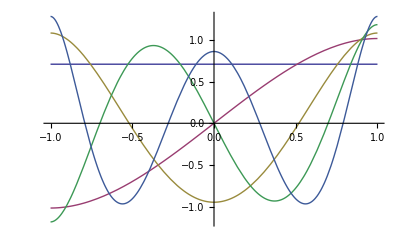

```mathematica
Plot[%,{x,-1,1}]
```

Alternatively, use TabView:

```mathematica
TabView@Table[n->Plot[vs⟦n+1⟧,{x,-1,1}],{n,0,4}]
```

12345

Clearly u_n(x) has n nodes in the interval [-1,1].